```mathematica
m=ℏ=g=1;
```

```mathematica
nmax=1000;
```

```mathematica
a=10;
```

```mathematica
Δ=a/(nmax+1);
```

```mathematica
xgrid=Range[nmax]*Δ;
```

```mathematica
W[x_]=m*g*x;
```

```mathematica
Wgrid=W/@xgrid;
```

```mathematica
groundstate[δβ_?NumericQ,κ_?NumericQ,tolerance_:10^-10]:=Module[{Ke,propKin,propPot2,prop,v0,γ,Ekin,Epot,Eint,Etot,μ},
(* compute the diagonal elements of exp[-δβ*T] *)
Ke=Exp[-δβ*Range[nmax]^2*(π^2 ℏ^2)/(2m a^2)]//N;
(* propagate by a full imaginary-time-step with T *)
propKin[v_]:=Normalize[FourierDST[Ke*FourierDST[v,1],1]];
(* propagate by a half imaginary-time-step with V *)
propPot2[v_]:=Normalize[Exp[-δβ/2*(Wgrid+κ*Abs[v]^2/Δ)]*v];
(* propagate by a full imaginary-time-step by *)
(* H=T+V using the Trotter approximation *)
prop[v_]:=propPot2[propKin[propPot2[v]]];
(* random starting point *)
v0=Normalize@RandomVariate[NormalDistribution[],nmax];
(* propagation to the ground state *)
γ=FixedPoint[prop,v0,SameTest->Function[{v1,v2},Norm[v1-v2]<tolerance]];
(* energy components *)
Ekin=(π^2 ℏ^2)/(2m a^2)(Range[nmax]^2).Abs[FourierDST[γ,1]]^2; (* kinetic *)
Epot=Wgrid.Abs[γ]^2; (* potential *)
Eint=κ/(2Δ)Total[Abs[γ]^4]; (* interaction *)
(* total energy *)
Etot=Ekin+Epot+Eint;
(* chemical potential *)
μ=Ekin+Epot+2Eint;
(* return energy, chemical potential, and ground-state coefficients *)
{Etot,μ,γ}]
```

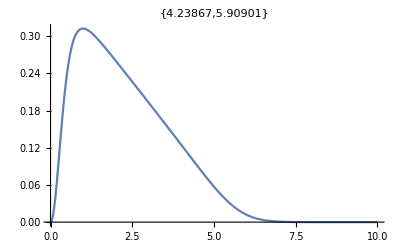

```mathematica
With[{κ=15*((g ℏ^4)/m)^(1/3),δβ=10^-4},
{Etot,μ,γ}=groundstate[δβ,κ];
ListLinePlot[Join[{{0,0}},{xgrid,Abs[γ]^2/Δ}ᵀ,{{a,0}}],PlotRange->All,PlotLabel->{Etot,μ}]]
```

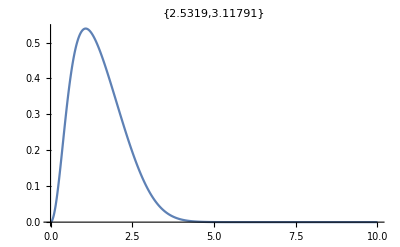

```mathematica
With[{κ=3*((g ℏ^4)/m)^(1/3),δβ=10^-4},
{Etot,μ,γ}=groundstate[δβ,κ];
ListLinePlot[Join[{{0,0}},{xgrid,Abs[γ]^2/Δ}ᵀ,{{a,0}}],PlotRange->All,PlotLabel->{Etot,μ}]]
```

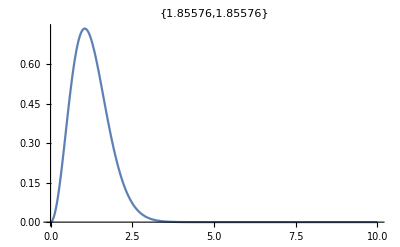

```mathematica
With[{κ=0*((g ℏ^4)/m)^(1/3),δβ=10^-4},
{Etot,μ,γ}=groundstate[δβ,κ];
ListLinePlot[Join[{{0,0}},{xgrid,Abs[γ]^2/Δ}ᵀ,{{a,0}}],PlotRange->All,PlotLabel->{Etot,μ}]]
```

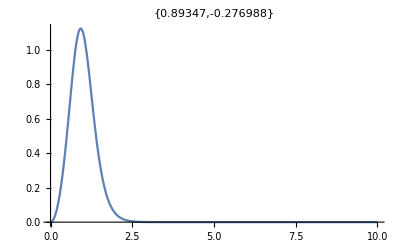

```mathematica
With[{κ=-3*((g ℏ^4)/m)^(1/3),δβ=10^-4},
{Etot,μ,γ}=groundstate[δβ,κ];
ListLinePlot[Join[{{0,0}},{xgrid,Abs[γ]^2/Δ}ᵀ,{{a,0}}],PlotRange->All,PlotLabel->{Etot,μ}]]
```

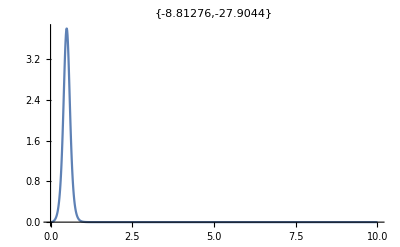

```mathematica
With[{κ=-15*((g ℏ^4)/m)^(1/3),δβ=10^-4},
{Etot,μ,γ}=groundstate[δβ,κ];
ListLinePlot[Join[{{0,0}},{xgrid,Abs[γ]^2/Δ}ᵀ,{{a,0}}],PlotRange->All,PlotLabel->{Etot,μ}]]
```